```mathematica
powerLaw[L_,lMin_, lMax_, alpha_]:=L^-alpha * Exp[-L/lMax]
```

```mathematica
unit=10^32;
avgCore[lMin_, lMax_, alpha_]:=unit*NIntegrate[L* powerLaw[L, lMin, lMax, alpha], {L, lMin, Infinity}]/NIntegrate[powerLaw[L, lMin, lMax, alpha], {L, lMin, Infinity}];
avg[lMin_,lMax_,alpha_]:=avgCore[lMin/unit,lMax/unit,alpha];
avg[10^29, 10^35, 1.94]
avg[10^29, 9*10^34, 1.8]
avg[9*10^31, 10^35, 1.5]
```

1.91022×10^30

5.29982×10^30

2.71039×10^33

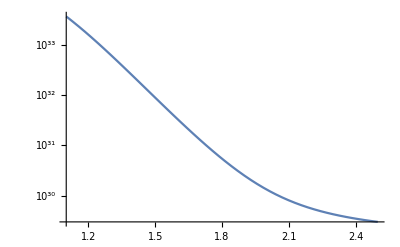

```mathematica
LogPlot[avg[10^29, 10^35,alpha],{alpha,1.1,2.5}]
```

```mathematica
truemap[lMax_,lMin_,alpha_]:=avg[lMin, lMax, alpha];
map[llmax_,llmin_,alpha_]:=Log10[truemap[10^llmax, 10^llmin, alpha]]
```

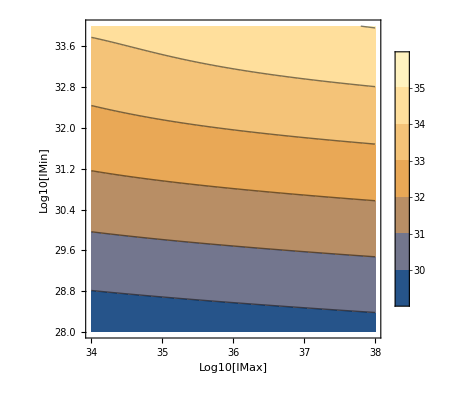

```mathematica
ContourPlot[map[lMax, lMin, 1.94],{lMax,34, 38}, {lMin,28, 34}, FrameLabel->{"Log10[lMax]","Log10[lMin]"},PlotLegends->Automatic]
```

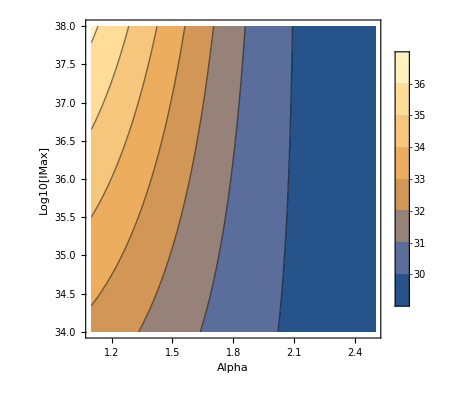

```mathematica
ContourPlot[map[lMax, 29, alpha], {alpha,1.1, 2.5},{lMax,34, 38}, FrameLabel->{"Alpha","Log10[lMax]"},PlotLegends->Automatic]
```